```mathematica
Import["/home/jadeleon/Documents/pce/mathematica/pce.m"]
```

## Definitions

```mathematica
a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};
```

## Hermanitos PCE

```mathematica
generatorsTwoQubits=ArrayReshape[Diagonal/@PCEgenerators[2],{15,4,4}];
```

```mathematica
OneFourthInvariantTwoQubits=Erase[generatorsTwoQubits,generatorsTwoQubits,4];
OneEigthInvariantTwoQubits=Erase[generatorsTwoQubits,OneFourthInvariantTwoQubits,2];
```

```mathematica
a//MatrixForm
```

(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1)

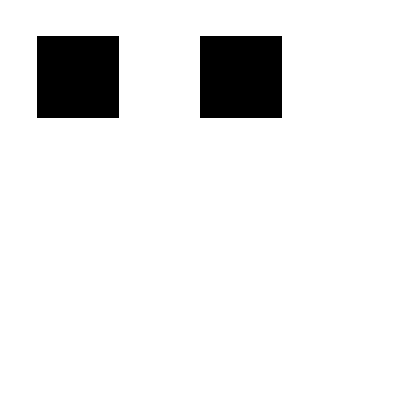

```mathematica
ArrayPlot[{{1,0,1,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}]
```

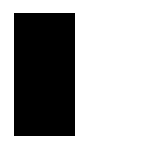
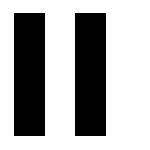
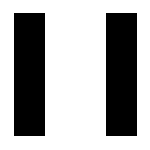
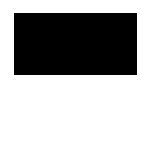
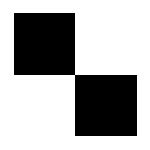
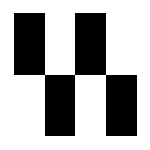
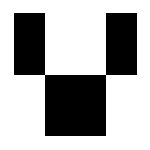
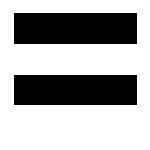

```mathematica
ArrayPlot[#,ImageSize->150]&/@generatorsTwoQubits
```

```mathematica
ArrayPlot[#,ImageSize->80]&/@OneFourthInvariantTwoQubits
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[KroneckerProduct[{1,1,1,1},{1,0,0,1}]+KroneckerProduct[{0,0,1,1},{0,0,0,0}],ImageSize->60],ArrayPlot[KroneckerProduct[{1,0,1,0},{1,1,1,1}]+KroneckerProduct[{0,1,0,1},{0,0,0,0}],ImageSize->60],ArrayPlot[KroneckerProduct[{1,0,0,1},{1,1,0,0}]+KroneckerProduct[{0,1,1,0},{0,0,1,1}],ImageSize->60]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ArrayPlot[KroneckerProduct[{1,1,0,0},{1,1,0,0}]+KroneckerProduct[{0,0,1,1},{0,0,1,1}],ImageSize->60],ArrayPlot[KroneckerProduct[{1,0,1,0},{1,0,1,0}]+KroneckerProduct[{0,1,0,1},{0,1,0,1}],ImageSize->60],ArrayPlot[KroneckerProduct[{1,0,0,1},{1,0,0,1}]+KroneckerProduct[{0,1,1,0},{0,1,1,0}],ImageSize->60]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
hermanitosOneHalfAndOneEigth={TwoQBoard@generatorsTwoQubits[[#[[1]]]],TwoQBoard@OneFourthInvariantTwoQubits[[#[[2]]]]}&/@{{1,4},{2,8},{3,12},{4,1},{8,1},{12,2},{5,5},{6,9},{7,13},{9,6},{10,10},{11,14},{13,7},{14,11},{15,15}};
```

```mathematica
hermanitosOneHalfAndOneEigth//Transpose//GraphicsGrid
```

-Graphics-

Nótese que los primeros 6 se pueden escribir de la forma ℰ⊗𝕀 o 𝕀⊗ℰ, con ℰ un canal cuántico PCE de 1 qubit.

```mathematica
KroneckerProduct[{1,1,0,0},{1,1,0,0}]+KroneckerProduct[{0,0,1,1},{0,0,1,1}]//TwoQBoard
```

-Graphics-

El resto son de la forma ℰ⊗ℰ+Λ, con Λ una operación que deja invariante el resto de las componentes.

```mathematica
KroneckerProduct[{1,0,1,0},{1,1,0,0}]//TwoQBoard
```

-Graphics-

```mathematica
OneQubitPCE={{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1}};
```

```mathematica
gen=ArrayReshape[ArrayPlot/@Flatten[Table[KroneckerProduct[OneQubitPCE[[i]],OneQubitPCE[[j]]]+KroneckerProduct[{1,1,1,1}-OneQubitPCE[[i]],{1,1,1,1}-OneQubitPCE[[j]]],{i,4},{j,4}],1],{2,8}];
```

```mathematica
DeleteDuplicates@ArrayReshape[Table[KroneckerProduct[KroneckerProduct[OneQubitPCE[[i]],OneQubitPCE[[j]]],OneQubitPCE[[k]]]+KroneckerProduct[KroneckerProduct[{1,1,1,1}-OneQubitPCE[[i]],{1,1,1,1}-OneQubitPCE[[j]]],{1,1,1,1}-OneQubitPCE[[k]]],{i,4},{j,4},{k,4}],{64,4,4,4}]//Length
```

64

```mathematica
Cube3q[Flatten@KroneckerProduct[{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{1,1,0,0}]+Flatten@KroneckerProduct[ConstantArray[1,{4,4}]-{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}},{1,1,1,1}-{1,1,0,0}]]
```

-Graphics3D-

```mathematica
Cube3q@ArrayReshape[KroneckerProduct[KroneckerProduct[OneQubitPCE[[1]],OneQubitPCE[[2]]],OneQubitPCE[[3]]]+KroneckerProduct[KroneckerProduct[{1,1,1,1}-OneQubitPCE[[1]],{1,1,1,1}-OneQubitPCE[[2]]],{1,1,1,1}-OneQubitPCE[[3]]],{4,4,4}]
```

-Graphics3D-

## Generadores de n qubits escritos como productos tensoriales de los generadores de 1 qubit

### 2 qubits

ℰ_i⊗ℰ_j+(𝟙-ℰ_i)⊗(𝟙-ℰ_j)
∑_(j∈𝒮) Φ_j_1⊗Φ_j_1⊗…⊗ℰ_j_n

```mathematica
(ℰ1⊗ℰ2)(𝟙-ℰ1)⊗(𝟙-ℰ2)//Expand
```

ℰ1⊗ℰ2 (-ℰ1+𝟙)⊗(-ℰ2+𝟙)

```mathematica
Table[2i,{i,0,4/2}]
```

{0,2,4}

```mathematica
𝒮=Subsets[{j1,j2,j3},{2}]
```

{{j1,j2},{j1,j3},{j2,j3}}

```mathematica
𝒮=Subsets[{𝟙-Subscript[ℰ, j1],𝟙-Subscript[ℰ, j2],𝟙-Subscript[ℰ, j3]},{2}]
```

{{𝟙-ℰ_j1,𝟙-ℰ_j2},{𝟙-ℰ_j1,𝟙-ℰ_j3},{𝟙-ℰ_j2,𝟙-ℰ_j3}}

```mathematica
ArrayPlot[#,ImageSize->100]&/@generatorsTwoQubits
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 3 qubits

Un canal PCE generador de 3 qubits se puede escribir de la forma 
			ℰ_i⊗ℰ_j⊗ℰ_k+(𝟙-ℰ_i)⊗(𝟙-ℰ_j)⊗ℰ_k+(𝟙-ℰ_i)⊗ℰ_j⊗(𝟙-ℰ_k)+ℰ_i⊗(𝟙-ℰ_j)⊗(𝟙-ℰ_k),
donde ℰ_i son canales cuánticos de 1 qubit. Sería bueno poder escribir esto de una manera más comprimida.

```mathematica
Flatten[Table[{i,j,k},{i,4},{j,4},{k,4}],2][[46]]
```

{3,4,2}

```mathematica
Generators3Qubits[i_,j_,k_]:=Module[{a},
a={{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1}};
KroneckerProduct[a[[k]],KroneckerProduct[a[[j]],a[[i]]]]+KroneckerProduct[a[[k]],KroneckerProduct[{1,1,1,1}-a[[j]],{1,1,1,1}-a[[i]]]]+KroneckerProduct[{1,1,1,1}-a[[k]],KroneckerProduct[a[[j]],{1,1,1,1}-a[[i]]]]+KroneckerProduct[{1,1,1,1}-a[[k]],KroneckerProduct[{1,1,1,1}-a[[j]],a[[i]]]]]
```

### 4 qubits

Un canal generador PCE de 4 qubits se puede escribir de la forma 
	ℰ_j_1⊗ℰ_j⊗ℰ_k⊗ℰ_l+(𝟙-ℰ_j_1)⊗(𝟙-ℰ_j)⊗ℰ_k⊗ℰ_l+(𝟙-ℰ_j_1)⊗ℰ_j⊗(𝟙-ℰ_k)⊗ℰ_l+(𝟙-ℰ_j_1)⊗ℰ_j⊗ℰ_k⊗(𝟙-ℰ_l)+ℰ_j_1⊗(𝟙-ℰ_j)⊗(𝟙-ℰ_k)⊗ℰ_l+ℰ_j_1⊗(𝟙-ℰ_j)⊗(𝟙-ℰ_k)⊗ℰ_l+ℰ_j_1⊗ℰ_j⊗(𝟙-ℰ_k)⊗(𝟙-ℰ_l)+(𝟙-ℰ_j_1)⊗(𝟙-ℰ_j)⊗(𝟙-ℰ_k)⊗(𝟙-ℰ_l),
donde ℰ_i son canales cuánticos de 1 qubit. Sería bueno poder escribir esto de una manera más comprimida.

```mathematica
Subsets[Range[3],{2}]
```

{{1,2},{1,3},{2,3}}

```mathematica
Part[Flatten[Table[{i,j,k,l},{i,4},{j,4},{k,4},{l,4}],3],231]
Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]
```

{4,3,2,3}

{1,3,5,7,10,12,14,16,18,20,22,24,25,27,29,31,33,35,37,39,42,44,46,48,50,52,54,56,57,59,61,63,66,68,70,72,73,75,77,79,81,83,85,87,90,92,94,96,98,100,102,104,105,107,109,111,113,115,117,119,122,124,126,128,130,132,134,136,137,139,141,143,145,147,149,151,154,156,158,160,162,164,166,168,169,171,173,175,177,179,181,183,186,188,190,192,193,195,197,199,202,204,206,208,210,212,214,216,217,219,221,223,225,227,229,231,234,236,238,240,242,244,246,248,249,251,253,255}

```mathematica
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,0,1,0},{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{1,3,5,7,33,35,37,39,193,195,197,199,225,227,229,231}

```mathematica
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,0},{1,1,1,1}-{1,0,1,0},{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{81,83,85,87,113,115,117,119,145,147,149,151,177,179,181,183}

```mathematica
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,0,1,0},{1,1,1,1}-{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{73,75,77,79,105,107,109,111,137,139,141,143,169,171,173,175}

```mathematica
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,0,1,0},{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{66,68,70,72,98,100,102,104,130,132,134,136,162,164,166,168}

```mathematica
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,1,1}-{1,0,1,0},{1,1,1,1}-{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{25,27,29,31,57,59,61,63,217,219,221,223,249,251,253,255}

```mathematica
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,1,1}-{1,0,1,0},{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{18,20,22,24,50,52,54,56,210,212,214,216,242,244,246,248}

```mathematica
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,0,1,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{10,12,14,16,42,44,46,48,202,204,206,208,234,236,238,240}

```mathematica
Intersection[Flatten@Position[Flatten@KroneckerProduct[{0,1,1,0},{0,1,0,1},{0,0,1,1},{0,1,0,1}],1],Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{90,92,94,96,122,124,126,128,154,156,158,160,186,188,190,192}

```mathematica
positions001={1,3,5,7,33,35,37,39,193,195,197,199,225,227,229,231}~Join~{81,83,85,87,113,115,117,119,145,147,149,151,177,179,181,183}~Join~{73,75,77,79,105,107,109,111,137,139,141,143,169,171,173,175}~Join~{66,68,70,72,98,100,102,104,130,132,134,136,162,164,166,168}~Join~{25,27,29,31,57,59,61,63,217,219,221,223,249,251,253,255}~Join~{18,20,22,24,50,52,54,56,210,212,214,216,242,244,246,248}~Join~{10,12,14,16,42,44,46,48,202,204,206,208,234,236,238,240}~Join~{90,92,94,96,122,124,126,128,154,156,158,160,186,188,190,192};
```

```mathematica
Intersection[positions001,Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]]
```

{1,3,5,7,10,12,14,16,18,20,22,24,25,27,29,31,33,35,37,39,42,44,46,48,50,52,54,56,57,59,61,63,66,68,70,72,73,75,77,79,81,83,85,87,90,92,94,96,98,100,102,104,105,107,109,111,113,115,117,119,122,124,126,128,130,132,134,136,137,139,141,143,145,147,149,151,154,156,158,160,162,164,166,168,169,171,173,175,177,179,181,183,186,188,190,192,193,195,197,199,202,204,206,208,210,212,214,216,217,219,221,223,225,227,229,231,234,236,238,240,242,244,246,248,249,251,253,255}

```mathematica
Flatten@Position[1/2(tensorPower[a,4][[231]]+ConstantArray[1,256]),1]//Length
```

128

### 5 qubits

```mathematica
Part[Flatten[Table[{j1,j2,j3,j4,j5},{j1,4},{j2,4},{j3,4},{j4,4},{j5,4}],4],855]
Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]//Length
```

{4,2,2,2,3}

512

```mathematica
Length[Union[Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,1,1,1}-{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,1,0,0},{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,1,1}-{1,1,0,0},{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,1,1}-{1,1,0,0},{1,1,0,0},{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,0,0},{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,1,1,1}-{1,1,0,0},{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,1,1,1}-{1,0,0,1},{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]],
Intersection[Flatten@Position[Flatten@KroneckerProduct[{1,0,0,1},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,1,0,0},{1,1,1,1}-{1,0,1,0}],1],Flatten@Position[1/2(tensorPower[a,5][[855]]+ConstantArray[1,4^5]),1]]
]
]
```

512

### n qubits

Dado un conjunto de índices {j1,j2,j3}, digamos {2,4,3}

```mathematica
g={OneQubitPCE[[2]],OneQubitPCE[[4]],OneQubitPCE[[3]]}
```

{{1,1,0,0},{1,0,0,1},{1,0,1,0}}

```mathematica
Map[Complement[{1,2,3},#]&,Subsets[{1,2,3},{2}]]
```

{{3},{2},{1}}

```mathematica
Map[Complement[{1,2,3,4},#]&,Subsets[{1,2,3,4},{2}]~Join~Subsets[{1,2,3,4},{4}]]
```

{{3,4},{2,4},{2,3},{1,4},{1,3},{1,2},{}}

```mathematica
{g}
Map[g[[#]]&,Map[Complement[{1,2,3},#]&,Subsets[{1,2,3},{2}]],{2}]
Map[{1,1,1,1}-g[[#]]&,Subsets[{1,2,3},{2}],{2}]
```

{{{1,1,0,0},{1,0,0,1},{1,0,1,0}}}

{{{1,0,1,0}},{{1,0,0,1}},{{1,1,0,0}}}

{{{0,0,1,1},{0,1,1,0}},{{0,0,1,1},{0,1,0,1}},{{0,1,1,0},{0,1,0,1}}}

```mathematica
Join[Subsets[Range[3],{2}],Map[Complement[Range[3],#]&,Subsets[Range[3],{2}]],2]
```

{{1,2,3},{1,3,2},{2,3,1}}

```mathematica
Map[Complement[Range[3],#]&,Subsets[Range[3],{2}]]
```

{{3},{2},{1}}

Unir las 3 listas anteriores:

```mathematica
g={OneQubitPCE[[2]],OneQubitPCE[[4]],OneQubitPCE[[3]]}
tensorProducts001={g}~Join~Join[Map[{1,1,1,1}-g[[#]]&,Subsets[Range[3],{2}],{2}],Map[g[[#]]&,Map[Complement[Range[3],#]&,Subsets[Range[3],{2}]],{2}],2]
ordering={Range[3]}~Join~(Ordering[#]&/@Join[Subsets[Range[3],{2}],Map[Complement[Range[3],#]&,Subsets[Range[3],{2}]],2])
tensorProducts001N=tensorProducts001[[#,ordering[[#]]]]&/@Range[4]
Flatten@Total[Apply[KroneckerProduct,#]&/@tensorProducts001N]
```

{{1,1,0,0},{1,0,0,1},{1,0,1,0}}

{{{1,1,0,0},{1,0,0,1},{1,0,1,0}},{{0,0,1,1},{0,1,1,0},{1,0,1,0}},{{0,0,1,1},{0,1,0,1},{1,0,0,1}},{{0,1,1,0},{0,1,0,1},{1,1,0,0}}}

{{1,2,3},{1,2,3},{1,3,2},{3,1,2}}

{{{1,1,0,0},{1,0,0,1},{1,0,1,0}},{{0,0,1,1},{0,1,1,0},{1,0,1,0}},{{0,0,1,1},{1,0,0,1},{0,1,0,1}},{{1,1,0,0},{0,1,1,0},{0,1,0,1}}}

{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1}

```mathematica
Count[Flatten@Total[Apply[KroneckerProduct,#]&/@tensorProducts001N],1]
```

32

#### Función para sacar el generado asociado a una componente

```mathematica
OneQubitPCE={{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1}};
generators[indices_]:=Module[{n,g,tensorProducts001,tensorProducts001N,noId,siId},
g=OneQubitPCE[[#]]&/@(indices+1);
n=Length[g];
noId=Map[Complement[Range[n],#]&,Flatten[Subsets[Range[n],{#}]&/@Range[2,n,2],1]];
siId=Flatten[Subsets[Range[n],{#}]&/@Range[2,n,2],1];
tensorProducts001={g}~Join~Join[Map[{1,1,1,1}-g[[#]]&,siId,{2}],Map[g[[#]]&,noId,{2}],2];
ordering={Range[n]}~Join~Map[Ordering[#]&,Join[siId,noId,2]];
tensorProducts001N=Map[tensorProducts001[[#,ordering[[#]]]]&,Range[Length[ordering]]];
Flatten@Total[Apply[KroneckerProduct,#]&/@tensorProducts001N]
]
Complement[Flatten[Table[generators[{i,j,k}],{i,0,3},{j,0,3},{k,0,3}],2],ReplacePart[#,Position[#,-1]->0]&[tensorPower[a,3]]]//Length
```

0

```mathematica
{1,2,3,4}+1
```

{2,3,4,5}

```mathematica
ArrayPlot[ArrayReshape[{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{4,4}],ImageSize->100]
```

-Graphics-

Cambiar:
1. Agregar n índices
2. Cambiar la potencia del tensorPower[a,n]
3. Cambiar el nivel al que se aplica el Flatten[algo,n-1]

```mathematica
Complement[Flatten[Table[generators[{j1,j2}],{j1,4},{j2,4}],1],ReplacePart[#,Position[#,-1]->0]&[tensorPower[a,2]]]//Length
Complement[Flatten[Table[generators[{j1,j2,j3}],{j1,4},{j2,4},{j3,4}],2],ReplacePart[#,Position[#,-1]->0]&[tensorPower[a,3]]]//Length
Complement[Flatten[Table[generators[{j1,j2,j3,j4}],{j1,4},{j2,4},{j3,4},{j4,4}],3],ReplacePart[#,Position[#,-1]->0]&[tensorPower[a,4]]]//Length
Complement[Flatten[Table[generators[{j1,j2,j3,j4,j5}],{j1,4},{j2,4},{j3,4},{j4,4},{j5,4}],4],ReplacePart[#,Position[#,-1]->0]&[tensorPower[a,5]]]//Length
```

0

0

0

«1 more identical outputs»

```mathematica
Complement[Flatten[Table[generators[{j1,j2,j3,j4,j5,j6}],{j1,4},{j2,4},{j3,4},{j4,4},{j5,4},{j6,4}],5],ReplacePart[#,Position[#,-1]->0]&[tensorPower[a,6]]]//Length
```

0

```mathematica
Complement[Flatten[Table[generatorsThreeQubits[{j1,j2,j3,j4}],{j1,4},{j2,4},{j3,4},{j4,4}],3],ReplacePart[#,Position[#,-1]->0]&[tensorPower[a,4]]]//Length
```

180

```mathematica
ArrayPlot[{{1,0,1,0},{0,1,0,1},{1,0,1,0},{0,1,0,1}},ImageSize->100]
```

-Graphics-

```mathematica
generators[{2,2,2}]
```

{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0,1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0,0,1,0,1,1,0,1,0}